```mathematica
trapezoid = Import["/home/dk0r/HW1/integration/trapezoid.csv"]
```

{{n,epsilon},{1,0.268293},{2,0.0731707},{3,0.037037},{4,0.0243902},{5,0.0185366},{6,0.0153568},{7,0.0134395},{8,0.0121951},{9,0.011342},«99982»,{99992,0.00813008},{99993,0.00813008},{99994,0.00813008},{99995,0.00813008},{99996,0.00813008},{99997,0.00813008},{99998,0.00813008},{99999,0.00813008},{100000,0.00813008}}

```mathematica
simpson = Import["/home/dk0r/HW1/integration/simpson.csv"]
```

{{n,epsilon},{2,0.00813008},{4,0.00813008},{6,0.00813008},{8,0.00813008},{10,0.00813008},{12,0.00813008},{14,0.00813008},{16,0.00813008},{18,0.00813008},{20,0.00813008},«9979»,{19980,0.00813008},{19982,0.00813008},{19984,0.00813008},{19986,0.00813008},{19988,0.00813008},{19990,0.00813008},{19992,0.00813008},{19994,0.00813008},{19996,0.00813008},{19998,0.00813008},{20000,0.00813008}}

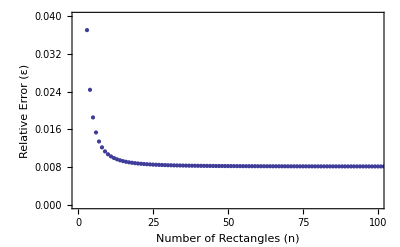

```mathematica
trapezoidx2 = ListPlot[trapezoid,
PlotRange->{{0,100},{0,0.04}},
Frame -> True,
LabelStyle->{FontSize->15},
FrameLabel->{"Number of Rectangles (n)", "Relative Error (ε)"}]
```

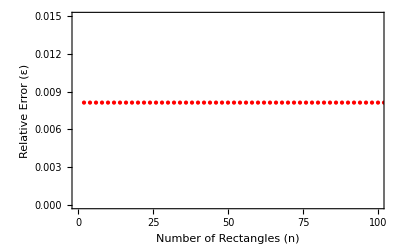

```mathematica
simpsonx2 = ListPlot[simpson,
PlotRange->{{0,100},{0,0.015}},
Frame -> True,
LabelStyle->{FontSize->15},
FrameLabel->{"Number of Rectangles (n)", "Relative Error (ε)"},
PlotStyle->Red]
```

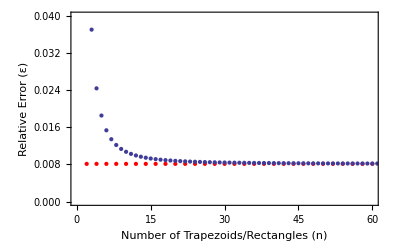

```mathematica
Show [{simpsonx2,trapezoidx2},
PlotRange->{{0,60},{0,0.04}},
Frame -> True,
LabelStyle->{FontSize->15},
FrameLabel->{"Number of Trapezoids/Rectangles (n)", "Relative Error (ε)"}]
```